```mathematica
test=stubbornForm;
```

```mathematica
Solve[{s03+s04+α1==α2,s02+s05+β1==β2,s01+s03+γ1==γ2,s02+s04+δ1==δ2,s01+s05+ϵ1==ϵ2},{α1,β1,γ1,δ1,ϵ1}]
```

{{α1→-s03-s04+α2,β1→-s02-s05+β2,γ1→-s01-s03+γ2,δ1→-s02-s04+δ2,ϵ1→-s01-s05+ϵ2}}

```mathematica
alfarep=First[Solve[{s03+s04+α1==α2,s02+s05+β1==β2,s01+s03+γ1==γ2,s02+s04+δ1==δ2,s01+s05+ϵ1==ϵ2},{α1,β1,γ1,δ1,ϵ1}]]
```

{α1→-s03-s04+α2,β1→-s02-s05+β2,γ1→-s01-s03+γ2,δ1→-s02-s04+δ2,ϵ1→-s01-s05+ϵ2}

```mathematica
alfarep={α1->1/2 (m1+m2+m3-m4-m5),β1->1/2 (-m1+m2+m3+m4-m5),γ1->1/2 (-m1-m2+m3+m4+m5),δ1->1/2 (m1-m2-m3+m4+m5),ϵ1->1/2 (m1+m2-m3-m4+m5)}
```

{α1→1/2 (m1+m2+m3-m4-m5),β1→1/2 (-m1+m2+m3+m4-m5),γ1→1/2 (-m1-m2+m3+m4+m5),δ1→1/2 (m1-m2-m3+m4+m5),ϵ1→1/2 (m1+m2-m3-m4+m5)}

```mathematica
alfarep={}
```

{}

```mathematica
Select[stubbornKeys,#≠K5Key&]//Length
```

4

```mathematica
ListofVars2[key_]:=ListofVars[test[key]["colofour3"]/.alfarep]
```

```mathematica
ListofVars[12]
```

ListQ::argx: ListQ called with 0 arguments; 1 argument is expected.

If[ListQ[],{Sequence[]}]

```mathematica
With[
{vars={α,β,γ,δ,ϵ,α1,β1,γ1,δ1,ϵ1}},Graph[Table [Map[#->jj&,Intersection[ListofVars2[jj],vars]],{jj,Select[Keys[test],ContainsAll[ListofVars[#],vars]&]}]//Flatten,VertexSize->Tiny]
]
```

ListQ::argx: ListQ called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListQ :: argx will be suppressed during this calculation.

-Graphics-

```mathematica
edges1=Table [Map[#->jj&,ListofVars2[jj]],{jj,Select[stubbornKeys,#≠K5Key&]}]//Flatten
```

{s14→364,s15→364,α→364,β→364,α1→364,β1→364,δ1→364,ϵ1→364,ζ→364,s08→367,s18→367,ϵ→367,γ1→367,s06→445,s16→445,γ→445,γ1→445,s01→448,s03→448,γ1→448}

```mathematica
edges1={s01->448,s03->448,γ1->448,s01->7738,γ1->7738,s14->9112,s15->9112,ζ->9112,s13->9598,s15->9598,ζ->9598,s15->9841,s01->11680,s05->11680,ϵ1->11680,s01->11950,ϵ1->11950,s03->22318,γ1->22318,s02->24922,s05->24922,β1->24922,s02->25168,β1->25168,s11->28794,s14->28794,ζ->28794,s14->28795,s12->29272,s13->29272,ζ->29272,s13->29281,s11->29514,s12->29514,ζ->29514,s12->29515,s11->29523,s11->29525,ζ->29525,s12->29533,ζ->29533,s17->29560,γ1->29608,s10->29633,s13->29767,ζ->29767,s09->29797,s14->30253,ζ->30253,s16->30334,s05->31444,ϵ1->31444,s05->31492,β1->31492,ϵ1->31714,β1->31738,s19->31954,s05->31984,s02->33834,s04->33834,δ1->33834,s02->33916,δ1->33916,s03->35406,s04->35406,α1->35406,s03->35434,α1->35434,s04->36030,δ1->36030,s20->36086,δ1->36112,s04->36138,α1->36138,α1->36166,s04->36194,s08->36817,s03->36898,s07->38281,s02->38308,s15->49207,ζ->49207,s18->49210,s06->51475,s01->51478}
```

{s01→448,s03→448,γ1→448,s01→7738,γ1→7738,s14→9112,s15→9112,ζ→9112,s13→9598,s15→9598,ζ→9598,s15→9841,s01→11680,s05→11680,ϵ1→11680,s01→11950,ϵ1→11950,s03→22318,γ1→22318,s02→24922,s05→24922,β1→24922,s02→25168,β1→25168,s11→28794,s14→28794,ζ→28794,s14→28795,s12→29272,s13→29272,ζ→29272,s13→29281,s11→29514,s12→29514,ζ→29514,s12→29515,s11→29523,s11→29525,ζ→29525,s12→29533,ζ→29533,s17→29560,γ1→29608,s10→29633,s13→29767,ζ→29767,s09→29797,s14→30253,ζ→30253,s16→30334,s05→31444,ϵ1→31444,s05→31492,β1→31492,ϵ1→31714,β1→31738,s19→31954,s05→31984,s02→33834,s04→33834,δ1→33834,s02→33916,δ1→33916,s03→35406,s04→35406,α1→35406,s03→35434,α1→35434,s04→36030,δ1→36030,s20→36086,δ1→36112,s04→36138,α1→36138,α1→36166,s04→36194,s08→36817,s03→36898,s07→38281,s02→38308,s15→49207,ζ→49207,s18→49210,s06→51475,s01→51478}

```mathematica
edges2={s06<->s15,s07<->s12,s08<->s14,s09<->s13,s10<->s11,s11<->s20,s12<->s17,s13<->s19,s14<->s16,s15<->s18,s01<->s06,s01<->s18,s02<->s07,s02<->s17,s03<->s08,s03<->s16,s04<->s10,s04<->s20,s05<->s09,s05<->s19}
test[448]["graph"]
```

{s06<->s15,s07<->s12,s08<->s14,s09<->s13,s10<->s11,s11<->s20,s12<->s17,s13<->s19,s14<->s16,s15<->s18,s01<->s06,s01<->s18,s02<->s07,s02<->s17,s03<->s08,s03<->s16,s04<->s10,s04<->s20,s05<->s09,s05<->s19}

-Graphics-

```mathematica
s01,s03,s05,s06,s07,s08,s09,s10,s11,s12,s13,s14,s15,s16,s17,s18,s19,s20
```

Syntax::tsntxi: "s01, s03, s05, s06, s07, s08, s09, s10, s11, s12, s13, s14, s15, s16, s17, s18, s19, s20" is incomplete; more input is needed.""

```mathematica
Graph[Join[edges1,edges2],GraphHighlight->Join[edges2,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}], VertexLabels->Join[Map[#->#&,{ζ,s01,s03,s05,s06,s07,s08,s09,s10,s11,s12,s13,s14,s15,s16,s17,s18,s19,s20,α1,β1,γ1,δ1,ϵ1}],Table [jj->Framed[Graph[test[jj,"graph"],ImageSize->{40,40}]],{jj,Select[stubbornKeys,#≠K5Key&]}]]]
```

Graph[{s01→448,s03→448,γ1→448,s01→7738,γ1→7738,s14→9112,s15→9112,ζ→9112,s13→9598,s15→9598,ζ→9598,s15→9841,s01→11680,s05→11680,ϵ1→11680,s01→11950,ϵ1→11950,s03→22318,γ1→22318,s02→24922,s05→24922,β1→24922,s02→25168,β1→25168,s11→28794,s14→28794,ζ→28794,s14→28795,s12→29272,s13→29272,ζ→29272,s13→29281,s11→29514,s12→29514,ζ→29514,s12→29515,s11→29523,s11→29525,ζ→29525,s12→29533,ζ→29533,s17→29560,γ1→29608,s10→29633,s13→29767,ζ→29767,s09→29797,s14→30253,ζ→30253,s16→30334,s05→31444,ϵ1→31444,s05→31492,β1→31492,ϵ1→31714,β1→31738,s19→31954,s05→31984,s02→33834,s04→33834,δ1→33834,s02→33916,δ1→33916,s03→35406,s04→35406,α1→35406,s03→35434,α1→35434,s04→36030,δ1→36030,s20→36086,δ1→36112,s04→36138,α1→36138,α1→36166,s04→36194,s08→36817,s03→36898,s07→38281,s02→38308,s15→49207,ζ→49207,s18→49210,s06→51475,s01→51478,s06<->s15,s07<->s12,s08<->s14,s09<->s13,s10<->s11,s11<->s20,s12<->s17,s13<->s19,s14<->s16,s15<->s18,s01<->s06,s01<->s18,s02<->s07,s02<->s17,s03<->s08,s03<->s16,s04<->s10,s04<->s20,s05<->s09,s05<->s19},GraphHighlight→{s06<->s15,s07<->s12,s08<->s14,s09<->s13,s10<->s11,s11<->s20,s12<->s17,s13<->s19,s14<->s16,s15<->s18,s01<->s06,s01<->s18,s02<->s07,s02<->s17,s03<->s08,s03<->s16,s04<->s10,s04<->s20,s05<->s09,s05<->s19,36166,31738,29608,36112,31714},VertexLabels→{ζ→ζ,s01→s01,s03→s03,s05→s05,s06→s06,s07→s07,s08→s08,s09→s09,s10→s10,s11→s11,s12→s12,s13→s13,s14→s14,s15→s15,s16→s16,s17→s17,s18→s18,s19→s19,s20→s20,α1→α1,β1→β1,γ1→γ1,δ1→δ1,ϵ1→ϵ1,364→-Graphics-,367→-Graphics-,445→-Graphics-,448→-Graphics-}]

```mathematica
test[alfa1Key]["colortable2"]//TableForm
```

0 | 1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ)
1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ) | 0
0 | 1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ)
0 | 1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ)
0 | 1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ)
1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ) | 0
0 | 1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ)
0 | 1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ)
0 | 1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ)
0 | 1/12 (4 b01-2 b03+4 b05-2 b07-2 b08-2 b09+2 b11-4 b12-4 b14+2 b15-4 b16+2 b17+2 b19-4 b20+2 b21+2 b22+2 b24+2 b25-4 b26+2 b28-4 b30+2 b32+2 b33+2 b34-b36-b37-b38-b39-b40+5 b41-b42-b43-b44+5 b45-b46-b47+b48-b49-b50+ζ)

```mathematica
ineqs3=Simplify[Fold[And,(ineqs/.{α1->1/2 (m1+m2+m3-m4-m5),β1->1/2 (-m1+m2+m3+m4-m5),γ1->1/2 (-m1-m2+m3+m4+m5),δ1->1/2 (m1-m2-m3+m4+m5),ϵ1->1/2 (m1+m2-m3-m4+m5)})/.alfarep]]
```

z>0&&v03>0&&z>v03&&v06>0&&v03+v06+v08>v02&&z>v06&&v02>0&&v02+v03+v08>v06&&v02+v06+v08>v03&&v08>0&&v02+v06>v03+v08&&v02+v03>v06+v08&&z>v02&&v03+v06>v02+v08&&v08+2 z>v02+v03+v06&&v04>0&&v03+v04+v09>v05&&v04+v06+v10>v01&&2 v03+2 v04+2 v06+2 v08+2 v09+2 v10+v14>v01+v02+v05+v07+v11+v12+v13&&v12>0&&2 v01+2 v03+2 v08+2 v09+5 v12+v14>v02+v04+v05+v06+v07+v10+v11+v13&&2 v05+2 v06+2 v08+2 v10+5 v12+v14>v01+v02+v03+v04+v07+v09+v11+v13&&v01+v03+v05+v06+4 v08+v09+v10+4 v12+2 v14>2 (v02+v04+v07+v11+v13)&&v04>v12&&v02+v03+4 v04+v06+v07+v09+v10+v11+v13>2 v01+2 v05+2 v08+5 v12+v14&&z>v04&&v02>v12&&v12+z>v02+v04&&v05>0&&v03+v05+v09>v04&&v13>0&&2 v01+2 v03+2 v08+2 v09+5 v13+v14>v02+v04+v05+v06+v07+v10+v11+v12&&v05>v13&&v02+v05+v07>v01&&2 v02+2 v03+2 v05+2 v07+2 v08+2 v09+v14>v01+v04+v06+v10+v11+v12+v13&&2 v02+2 v04+2 v07+2 v08+5 v13+v14>v01+v03+v05+v06+v09+v10+v11+v12&&v01+v02+v03+v04+v07+4 v08+v09+4 v13+2 v14>2 (v05+v06+v10+v11+v12)&&v02+v03+4 v05+v06+v07+v09+v10+v11+v12>2 v01+2 v04+2 v08+5 v13+v14&&v04+v05+v09>v03&&v09>0&&v04+v05>v03+v09&&2 v02+2 v04+2 v09+2 v10+5 v13+v14>v01+v03+v05+v06+v07+v08+v11+v12&&v01+v02+v03+v04+v08+4 v09+v10+4 v13+2 v14>2 (v05+v06+v07+v11+v12)&&2 v05+2 v06+2 v07+2 v09+5 v12+v14>v01+v02+v03+v04+v08+v10+v11+v13&&v01+v03+v05+v06+v07+v08+4 v09+4 v12+2 v14>2 (v02+v04+v10+v11+v13)&&v12+v13+v14>v11&&2 (v01+v03+v08+v09+v12+v13+2 v14)>v02+v04+v05+v06+v07+v10+4 v11&&v02+v04+v05+v06+v07+v10+v11+v12+v13>2 v01+2 v03+2 v08+2 v09+v14&&v03+v05>v04+v09&&4 v02+v03+v04+v05+v07+v08+v10+v11+v13>2 v01+2 v06+2 v09+5 v12+v14&&z>v05&&v06>v13&&v13+z>v05+v06&&v03+v04>v05+v09&&v03+v04+v05+4 v06+v07+v08+v10+v11+v12>2 v01+2 v02+2 v09+5 v13+v14&&v09+2 z>v03+v04+v05&&v01>0&&v11>0&&v01>v11&&v01+v06+v10>v04&&2 v05+2 v06+2 v08+2 v10+5 v11+v14>v01+v02+v03+v04+v07+v09+v12+v13&&v01+v02+v07>v05&&2 v02+2 v04+2 v07+2 v08+5 v11+v14>v01+v03+v05+v06+v09+v10+v12+v13&&2 v01+2 v02+2 v06+2 v07+2 v08+2 v10+v14>v03+v04+v05+v09+v11+v12+v13&&v02+v04+v05+v06+v07+4 v08+v10+4 v11+2 v14>2 (v01+v03+v09+v12+v13)&&4 v01+v02+v03+v06+v07+v09+v10+v12+v13>2 v04+2 v05+2 v08+5 v11+v14&&v01+v04+v10>v06&&2 v02+2 v04+2 v09+2 v10+5 v11+v14>v01+v03+v05+v06+v07+v08+v12+v13&&v10>0&&v02+v04+v05+v06+v08+v09+4 v10+4 v11+2 v14>2 (v01+v03+v07+v12+v13)&&v01+v04>v06+v10&&2 v01+2 v03+2 v07+2 v10+5 v12+v14>v02+v04+v05+v06+v08+v09+v11+v13&&v11+v12+v14>v13&&v01+v03+v05+v06+v07+v08+4 v10+4 v12+2 v14>2 (v02+v04+v09+v11+v13)&&2 (v05+v06+v08+v10+v11+v12+2 v14)>v01+v02+v03+v04+v07+v09+4 v13&&v01+v02+v03+v04+v07+v09+v11+v12+v13>2 v05+2 v06+2 v08+2 v10+v14&&v01+v06>v04+v10&&v01+4 v02+v04+v06+v07+v08+v09+v11+v13>2 v03+2 v05+2 v10+5 v12+v14&&v01+v05+v07>v02&&2 v05+2 v06+2 v07+2 v09+5 v11+v14>v01+v02+v03+v04+v08+v10+v12+v13&&2 v01+2 v03+2 v07+2 v10+5 v13+v14>v02+v04+v05+v06+v08+v09+v11+v12&&v11+v13+v14>v12&&v07>0&&v02+v04+v05+v06+4 v07+v08+v09+4 v11+2 v14>2 (v01+v03+v10+v12+v13)&&v01+v02+v03+v04+4 v07+v08+v10+4 v13+2 v14>2 (v05+v06+v09+v11+v12)&&2 (v02+v04+v07+v08+v11+v13+2 v14)>v01+v03+v05+v06+v09+v10+4 v12&&v01+v05>v02+v07&&v01+v03+v05+v06+v09+v10+v11+v12+v13>2 v02+2 v04+2 v07+2 v08+v14&&2 v01+2 v04+2 v05+2 v07+2 v09+2 v10+v14>v02+v03+v06+v08+v11+v12+v13&&v02+v04+v05+v06+v07+4 v09+v10+4 v11+2 v14>2 (v01+v03+v08+v12+v13)&&4 v01+v03+v04+v05+v07+v08+v10+v12+v13>2 v02+2 v06+2 v09+5 v11+v14&&v01+v02+v03+v04+v07+v09+4 v10+4 v13+2 v14>2 (v05+v06+v08+v11+v12)&&2 (v02+v04+v09+v10+v11+v13+2 v14)>v01+v03+v05+v06+v07+v08+4 v12&&v01+v04+4 v05+v06+v07+v08+v09+v11+v12>2 v02+2 v03+2 v10+5 v13+v14&&v01+v03+v05+v06+4 v07+v09+v10+4 v12+2 v14>2 (v02+v04+v08+v11+v13)&&2 (v05+v06+v07+v09+v11+v12+2 v14)>v01+v02+v03+v04+v08+v10+4 v13&&2 (v01+v03+v07+v10+v12+v13+2 v14)>v02+v04+v05+v06+v08+v09+4 v11&&v14≥0&&2 (v01+v03+v07+v10+v12+v13)>v02+v04+v05+v06+v08+v09+4 v11+2 v14&&2 (v05+v06+v07+v09+v11+v12)≥v01+v02+v03+v04+v08+v10+4 v13+2 v14&&v01+v02+4 v04+v05+v08+v09+v10+v11+v13>2 v03+2 v06+2 v07+5 v12+v14&&2 (v02+v04+v09+v10+v11+v13)>v01+v03+v05+v06+v07+v08+4 v12+2 v14&&2 v01+2 v04+2 v05+2 v08+v14>v02+v03+v06+v07+v09+v10+v11+v12+v13&&v01+v03+v05+v06+v07+v08+v11+v12+v13>2 v02+2 v04+2 v09+2 v10+v14&&2 (v02+v04+v07+v08+v11+v13)>v01+v03+v05+v06+v09+v10+4 v12+2 v14&&2 v01+2 v03+2 v05+2 v06+5 v12+v14>4 v02+4 v04+v07+v08+v09+v10+v11+v13&&v01+v02>v05+v07&&v01+v02+v05+4 v06+v08+v09+v10+v11+v12>2 v03+2 v04+2 v07+5 v13+v14&&v01+v02+v03+v04+v08+v10+v11+v12+v13>2 v05+2 v06+2 v07+2 v09+v14&&2 (v05+v06+v08+v10+v11+v12)≥v01+v02+v03+v04+v07+v09+4 v13+2 v14&&2 v01+2 v02+2 v03+2 v04+5 v13+v14≥4 v05+4 v06+v07+v08+v09+v10+v11+v12&&2 v01+2 v02+2 v06+2 v09+v14>v03+v04+v05+v07+v08+v10+v11+v12+v13&&z>v01&&v03>v11&&v11+z>v01+v03&&v04+v06>v01+v10&&v01+4 v03+v04+v06+v07+v08+v09+v12+v13>2 v02+2 v05+2 v10+5 v11+v14&&v10+2 z>v01+v04+v06&&v02+v05>v01+v07&&v01+v02+4 v03+v05+v08+v09+v10+v12+v13>2 v04+2 v06+2 v07+5 v11+v14&&v02+v04+v05+v06+v08+v09+v11+v12+v13>2 v01+2 v03+2 v07+2 v10+v14&&2 (v01+v03+v08+v09+v12+v13)>v02+v04+v05+v06+v07+v10+4 v11+2 v14&&2 v02+2 v04+2 v05+2 v06+5 v11+v14>4 v01+4 v03+v07+v08+v09+v10+v12+v13&&2 v02+2 v03+2 v05+2 v10+v14>v01+v04+v06+v07+v08+v09+v11+v12+v13&&v07+2 z>v01+v02+v05&&2 v03+2 v04+2 v06+2 v07+v14>v01+v02+v05+v08+v09+v10+v11+v12+v13&&v07+v08+v09+v10+v11+v12+v13+6 z>2 v01+2 v02+2 v03+2 v04+2 v05+2 v06+v14

```mathematica
alfarep
```

{}

```mathematica
ExpressionToTable2[ineqs3]
```

v01>0
v02>0
v03>0
v04>0
v05>0
v06>0
v07>0
v08>0
v09>0
v10>0
v11>0
v12>0
v13>0
v14≥0
z>0
v01>v11
z>v01
v02>v12
z>v02
v03>v11
z>v03
v04>v12
z>v04
v05>v13
z>v05
v06>v13
z>v06
v02+v05+v07>v01
v01+v05+v07>v02
v01+v02+v07>v05
v02+v05>v01+v07
v01+v05>v02+v07
v01+v02>v05+v07
v11+z>v01+v03
v04+v06+v10>v01
v01+v06+v10>v04
v01+v04+v10>v06
v04+v06>v01+v10
v01+v06>v04+v10
v01+v04>v06+v10
v03+v06+v08>v02
v02+v06+v08>v03
v02+v03+v08>v06
v03+v06>v02+v08
v02+v06>v03+v08
v02+v03>v06+v08
v12+z>v02+v04
v04+v05+v09>v03
v03+v05+v09>v04
v03+v04+v09>v05
v04+v05>v03+v09
v03+v05>v04+v09
v03+v04>v05+v09
v13+z>v05+v06
v12+v13+v14>v11
v11+v13+v14>v12
v11+v12+v14>v13
v07+2 z>v01+v02+v05
v08+2 z>v02+v03+v06
v09+2 z>v03+v04+v05
v10+2 z>v01+v04+v06
2 v01+2 v02+2 v03+2 v04+5 v13+v14≥4 v05+4 v06+v07+v08+v09+v10+v11+v12
2 (v05+v06+v08+v10+v11+v12)≥v01+v02+v03+v04+v07+v09+4 v13+2 v14
2 (v05+v06+v07+v09+v11+v12)≥v01+v02+v03+v04+v08+v10+4 v13+2 v14
v01+v02+v03+v04+v07+v09+4 v10+4 v13+2 v14>2 (v05+v06+v08+v11+v12)
v01+v02+v03+v04+v08+4 v09+v10+4 v13+2 v14>2 (v05+v06+v07+v11+v12)
v01+v02+v03+v04+4 v07+v08+v10+4 v13+2 v14>2 (v05+v06+v09+v11+v12)
v01+v02+v03+v04+v07+4 v08+v09+4 v13+2 v14>2 (v05+v06+v10+v11+v12)
2 (v01+v03+v07+v10+v12+v13+2 v14)>v02+v04+v05+v06+v08+v09+4 v11
2 (v01+v03+v08+v09+v12+v13+2 v14)>v02+v04+v05+v06+v07+v10+4 v11
2 (v02+v04+v09+v10+v11+v13+2 v14)>v01+v03+v05+v06+v07+v08+4 v12
2 (v02+v04+v07+v08+v11+v13+2 v14)>v01+v03+v05+v06+v09+v10+4 v12
v01+v03+v05+v06+v07+v08+4 v10+4 v12+2 v14>2 (v02+v04+v09+v11+v13)
v01+v03+v05+v06+4 v08+v09+v10+4 v12+2 v14>2 (v02+v04+v07+v11+v13)
v01+v03+v05+v06+4 v07+v09+v10+4 v12+2 v14>2 (v02+v04+v08+v11+v13)
v01+v03+v05+v06+v07+v08+4 v09+4 v12+2 v14>2 (v02+v04+v10+v11+v13)
2 (v05+v06+v08+v10+v11+v12+2 v14)>v01+v02+v03+v04+v07+v09+4 v13
2 (v05+v06+v07+v09+v11+v12+2 v14)>v01+v02+v03+v04+v08+v10+4 v13
v02+v04+v05+v06+v08+v09+4 v10+4 v11+2 v14>2 (v01+v03+v07+v12+v13)
v02+v04+v05+v06+v07+4 v09+v10+4 v11+2 v14>2 (v01+v03+v08+v12+v13)
v02+v04+v05+v06+v07+4 v08+v10+4 v11+2 v14>2 (v01+v03+v09+v12+v13)
v02+v04+v05+v06+4 v07+v08+v09+4 v11+2 v14>2 (v01+v03+v10+v12+v13)
2 v02+2 v04+2 v09+2 v10+5 v13+v14>v01+v03+v05+v06+v07+v08+v11+v12
2 v01+2 v03+2 v07+2 v10+5 v13+v14>v02+v04+v05+v06+v08+v09+v11+v12
2 v01+2 v03+2 v08+2 v09+5 v13+v14>v02+v04+v05+v06+v07+v10+v11+v12
2 v02+2 v04+2 v07+2 v08+5 v13+v14>v01+v03+v05+v06+v09+v10+v11+v12
2 v05+2 v06+2 v08+2 v10+5 v12+v14>v01+v02+v03+v04+v07+v09+v11+v13
2 v01+2 v03+2 v07+2 v10+5 v12+v14>v02+v04+v05+v06+v08+v09+v11+v13
2 v01+2 v03+2 v08+2 v09+5 v12+v14>v02+v04+v05+v06+v07+v10+v11+v13
2 v05+2 v06+2 v07+2 v09+5 v12+v14>v01+v02+v03+v04+v08+v10+v11+v13
2 v01+2 v03+2 v05+2 v06+5 v12+v14>4 v02+4 v04+v07+v08+v09+v10+v11+v13
2 v02+2 v04+2 v09+2 v10+5 v11+v14>v01+v03+v05+v06+v07+v08+v12+v13
2 v05+2 v06+2 v08+2 v10+5 v11+v14>v01+v02+v03+v04+v07+v09+v12+v13
2 v05+2 v06+2 v07+2 v09+5 v11+v14>v01+v02+v03+v04+v08+v10+v12+v13
2 v02+2 v04+2 v07+2 v08+5 v11+v14>v01+v03+v05+v06+v09+v10+v12+v13
2 v02+2 v04+2 v05+2 v06+5 v11+v14>4 v01+4 v03+v07+v08+v09+v10+v12+v13
2 v03+2 v04+2 v06+2 v08+2 v09+2 v10+v14>v01+v02+v05+v07+v11+v12+v13
2 v01+2 v04+2 v05+2 v07+2 v09+2 v10+v14>v02+v03+v06+v08+v11+v12+v13
2 v01+2 v02+2 v06+2 v07+2 v08+2 v10+v14>v03+v04+v05+v09+v11+v12+v13
2 v02+2 v03+2 v05+2 v10+v14>v01+v04+v06+v07+v08+v09+v11+v12+v13
2 v02+2 v03+2 v05+2 v07+2 v08+2 v09+v14>v01+v04+v06+v10+v11+v12+v13
2 v01+2 v02+2 v06+2 v09+v14>v03+v04+v05+v07+v08+v10+v11+v12+v13
2 v01+2 v04+2 v05+2 v08+v14>v02+v03+v06+v07+v09+v10+v11+v12+v13
2 v03+2 v04+2 v06+2 v07+v14>v01+v02+v05+v08+v09+v10+v11+v12+v13
v01+v03+v05+v06+v09+v10+v11+v12+v13>2 v02+2 v04+2 v07+2 v08+v14
v01+v02+v03+v04+v08+v10+v11+v12+v13>2 v05+2 v06+2 v07+2 v09+v14
v02+v04+v05+v06+v07+v10+v11+v12+v13>2 v01+2 v03+2 v08+2 v09+v14
v02+v04+v05+v06+v08+v09+v11+v12+v13>2 v01+2 v03+2 v07+2 v10+v14
v01+v02+v03+v04+v07+v09+v11+v12+v13>2 v05+2 v06+2 v08+2 v10+v14
v01+v03+v05+v06+v07+v08+v11+v12+v13>2 v02+2 v04+2 v09+2 v10+v14
v01+v02+4 v03+v05+v08+v09+v10+v12+v13>2 v04+2 v06+2 v07+5 v11+v14
4 v01+v02+v03+v06+v07+v09+v10+v12+v13>2 v04+2 v05+2 v08+5 v11+v14
4 v01+v03+v04+v05+v07+v08+v10+v12+v13>2 v02+2 v06+2 v09+5 v11+v14
2 (v01+v03+v07+v10+v12+v13)>v02+v04+v05+v06+v08+v09+4 v11+2 v14
v01+4 v03+v04+v06+v07+v08+v09+v12+v13>2 v02+2 v05+2 v10+5 v11+v14
2 (v01+v03+v08+v09+v12+v13)>v02+v04+v05+v06+v07+v10+4 v11+2 v14
v01+v02+4 v04+v05+v08+v09+v10+v11+v13>2 v03+2 v06+2 v07+5 v12+v14
v02+v03+4 v04+v06+v07+v09+v10+v11+v13>2 v01+2 v05+2 v08+5 v12+v14
2 (v02+v04+v09+v10+v11+v13)>v01+v03+v05+v06+v07+v08+4 v12+2 v14
4 v02+v03+v04+v05+v07+v08+v10+v11+v13>2 v01+2 v06+2 v09+5 v12+v14
v01+4 v02+v04+v06+v07+v08+v09+v11+v13>2 v03+2 v05+2 v10+5 v12+v14
2 (v02+v04+v07+v08+v11+v13)>v01+v03+v05+v06+v09+v10+4 v12+2 v14
v01+v02+v05+4 v06+v08+v09+v10+v11+v12>2 v03+2 v04+2 v07+5 v13+v14
v02+v03+4 v05+v06+v07+v09+v10+v11+v12>2 v01+2 v04+2 v08+5 v13+v14
v03+v04+v05+4 v06+v07+v08+v10+v11+v12>2 v01+2 v02+2 v09+5 v13+v14
v01+v04+4 v05+v06+v07+v08+v09+v11+v12>2 v02+2 v03+2 v10+5 v13+v14
v07+v08+v09+v10+v11+v12+v13+6 z>2 v01+2 v02+2 v03+2 v04+2 v05+2 v06+v14

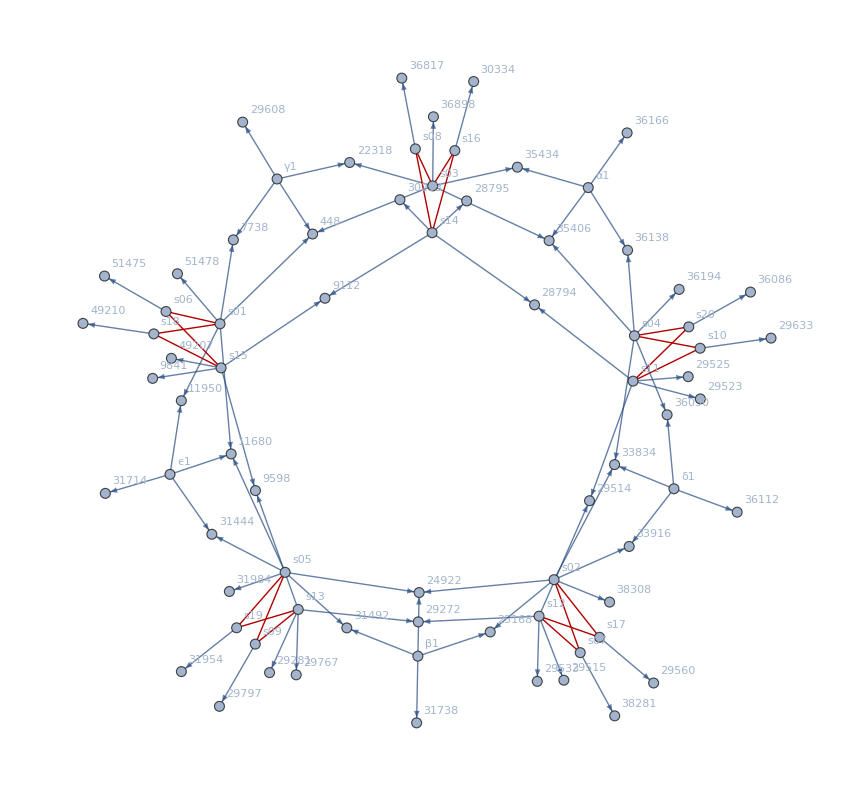

```mathematica
VertexDelete[Graph[Join[edges1,edges2],GraphHighlight->edges2, VertexLabels->"Name"],ζ]
```

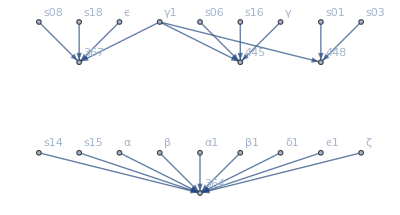

```mathematica
Graph[Table [Map[#->jj&,With[{kk=getAllVariables[test[jj]["colofour3"]]},If[ListQ[kk],kk,{kk}]]],{jj,Select[stubbornKeys,#≠K5Key&]}]//Flatten, VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

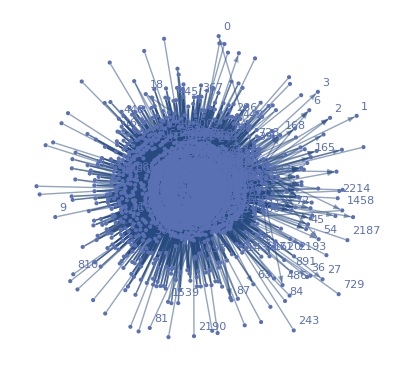

```mathematica
Graph[Table [Map[#->jj&,With[{kk=getAllVariables[test[jj]["colofour3"]]},If[ListQ[kk],kk,{kk}]]],{jj,Keys[test]}]//Flatten, VertexLabels->"Name"]
```

```mathematica
Table [jj->With[{kk=getAllVariables[test2[jj]["colofour3"]]},If[ListQ[kk],kk,{kk}]],{jj,stubbornKeys}]//TableForm
```

364→{test2[364][colofour3]}
367→{test2[367][colofour3]}
445→{test2[445][colofour3]}
448→{test2[448][colofour3]}

```mathematica
With[
{vars={α,β,γ,δ,ϵ,α1,β1,γ1,δ1,ϵ1}},Select[Keys[test],ContainsAll[ListofVars[#],vars]&]//Length
]
```

ListQ::argx: ListQ called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListQ :: argx will be suppressed during this calculation.

0

```mathematica
Sort[Tally[Flatten[Table[ListofVars[k],{k,Keys[test]}]]],#1[[2]]>#2[[2]]&]//TableForm
```

ListQ::argx: ListQ called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListQ :: argx will be suppressed during this calculation.

If[ListQ[],{Sequence[]}] | 1895